# EDMD Built

## Initialization

### Numerical Variable Definition

```mathematica
eventspercycle = 100; (*Events per sphere per cycle*)
n=300; (*Number of Spheres*)
steps=eventspercycle n; (*steps per cycle*)
ipf=.3; (*Initial packing fraction*)
rate=.001; (*Growth rate (relative)*)
mpressure=100; (*max pressure*)
gtime = 0 ;(*global time*)
bratio = .4;
rratio = .4;
size = 1;
steps=eventspercycle n; (*steps per cycle*)
```

### Global Variables

Initializes radii, positions, velocities, nextevents, heap, hash, cellMatrix, cellA, lastupdates in that order.

```mathematica
gtime=0;
radii=rlist[ipf, size, n, bratio, rratio];
nrows=optimalGrid[size, radii⟦1⟧];
positions=createDisks[radii, size];
velocities = velocityInit[size, n];
setInitialEvents[n]
changeBins[nrows]
lastupdates=Table[0, n];
nestpositions={positions};
nestradii={radii};
pf={packingFraction};
```

### Process Variables

```mathematica
nchecks=0;
ntrans=0;
ncollisions = 0;
counter = 0;
nevents=0;
```

## Process

### Step

Processes a single event.

```mathematica
nextevents
```

{{0,1,∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
processEvent
```

check event error

```mathematica
nextevents
```

{{0.,1,-∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
obtainMin@heap
```

{0,2}

```mathematica
(processEvent//AbsoluteTiming)⟦1⟧
```

0.00238216

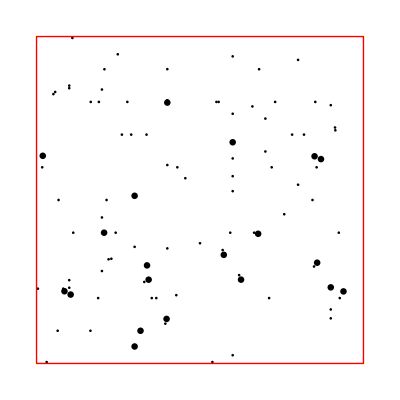

```mathematica
displayParticles[positions, radii, size]
```

### Cycle

```mathematica
positions=positions+velocities(gtime-lastupdates);
```

```mathematica
radii=radii(1+gtime rate);
```

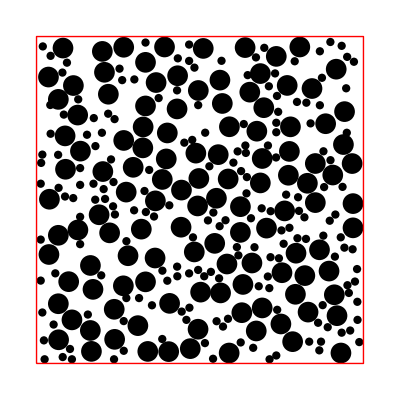

```mathematica
displayParticles[positions, radii, size]
```

```mathematica
overlapQ
```

False

```mathematica
radii[[1]]
```

0.0316228

```mathematica
nextevents
```

{{201.505,1,∞},{201.505,2,6},{201.507,3,5}}

```mathematica
nevents=0;
(Process[];)//AbsoluteTiming
```

check event error

check event error

check event error

«10 more identical outputs»

$Aborted

```mathematica
nevents
```

30001

```mathematica
pf
```

{0.467469,0.468442,0.469543,0.470573,0.471654,0.472694,0.473773,0.474828,0.475885,0.47692,0.477942}

```mathematica
positionsz=positions+velocities(gtime - lastupdates);
positionsz[[51]]
```

```mathematica
lastupdates[[49]]
```

```mathematica
positions[]
```

0.17811

```mathematica
For[i=1, i<n, i++,
For[j=i+1, j≤n, j++,
If[!overlapC[{positionsz⟦i⟧, radii⟦i⟧}, {positionsz⟦j⟧, radii⟦j⟧}],
Print[i," ", j]
]
]
]
```

49 51

```mathematica
nextevents[[51]]
```

{0.252677,51,304}

```mathematica
gtime
```

0.252677

```mathematica
cellA[49]
```

{11,2}

```mathematica
findNextCollision[49]
```

969 already overlapping, C, d:-0.000484102 0.0000797094

spheres are already overlapping

$Aborted

```mathematica
nextevents[[51]]
```

{0.252677,51,304}

```mathematica
Norm[positionsz⟦51⟧-positionsz⟦49⟧]
```

0.0593121

0.0039335

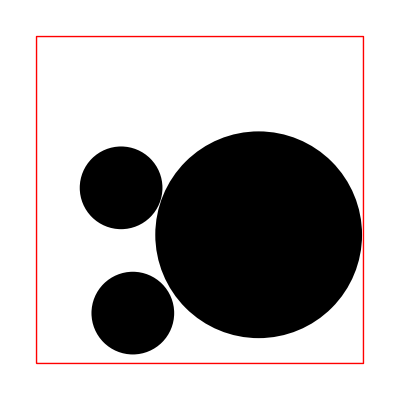

```mathematica
radii[[49]]+radii[[51]]-%
```

```mathematica
overlapQ
```

True

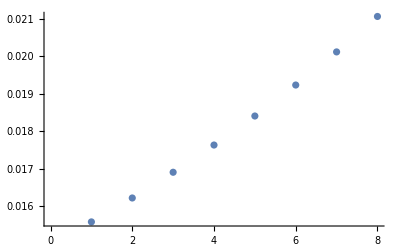

```mathematica
ListPlot@pf
```

```mathematica
pf//Length
```

19

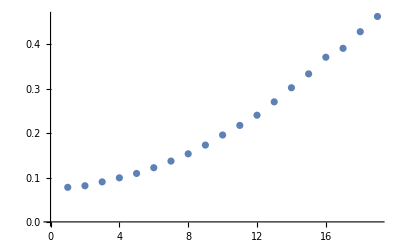

```mathematica
ListPlot@pf
```

```mathematica
nrows
```

9